# The Hamiltonian in the Post-Minkowski Approximation

A notebook dedicated to calculating the equations necessary for the Post-Minkowski approximation of the Hamiltonian. This is another method of approximated general relativistic effects, though not as commonly used as the Post-Newtonian approximation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Basic definitions

This cell evaluates some of the basic definitions that are used in the equations. ndim represents the number of dimension, nbody the number of bodies in the simulation. position is a list containing the x, y, and z (depending on the number of dimensions) positions of each body. p is another vector, containing the x, y, and z components of momentum for each body. m is another list, which contains the masses of all three bodies.

```mathematica
ndim=2;
nbody=2;
If[ndim==2,
position={{qax,qay},{qbx,qby}};
p={{pax,pay},{pbx,pby}};
m={ma,mb};
xdot={{qaxdot1,qaydot1},{qbxdot1,qbydot1}};
pdot={{paxdot1,paydot1},{pbxdot1,pbydot1}};
,
position={{qax,qay,qaz},{qbx,qby,qbz}};
p={{pax,pay,paz},{pbx,pby,pbz}};
m={ma,mb};
xdot={{qaxdot1,qaydot1,qazdot1},{qbxdot1,qbydot1,qbzdot1}};
pdot={{paxdot1,paydot1,pazdot1},{pbxdot1,pbydot1,pbzdot1}};
]
If[nbody==3,
If[ndim==3,
AppendTo[position,{qcx,qcy,qcz}];
AppendTo[p,{pcx,pcy,pcz}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1,qczdot1}];
AppendTo[pdot,{pcxdot1,pcydot1,pczdot1}];
,
AppendTo[position,{qcx,qcy}];
AppendTo[p,{pcx,pcy}];
AppendTo[m,mc];
AppendTo[xdot,{qcxdot1,qcydot1}];
AppendTo[pdot,{pcxdot1,pcydot1}];
]
]
```

## Functions

These functions listed are used for writing the PM approximation in Mathematica code. They allow for different vector operations. As well, two special functions, mline and y are defined, which correspond to two values in the PM approximation.

```mathematica
Normv[x_List] := Sqrt[x.x]
Normvector[x_List] := x/Normv[x]
rab[a_Integer,b_Integer] := position[[a]] - position[[b]]
Normvsq[x_List] := x.x
nhat[a_Integer,b_Integer] := Normvector[rab[a,b]]
nhatx[a_Integer,b_Integer,i_Integer] := nhat[a,b][[i]]
rdot[a_Integer,b_Integer] := xdot[[a]] - xdot[[b]]
R[a_Integer,b_Integer] :=Normv[rab[a,b]]
psq[a_Integer] := p[[a]].p[[a]]
mline[a_Integer]:=√(m[[a]]^2+psq[a])
y[a_Integer,b_Integer]:=mline[a]^-1 √(m[[a]]^2+(nhat[a,b].p[[a]])^2)
```

## The Hamiltonian

The PM Hamiltonian is defined here, to first order in G. These equations are taken from a 2008 paper by Ledvinka, Schafer, and Bicak. I have broken it up into four separate terms that are summed together to give the equation to first order in G.

```mathematica
W=ConstantArray[0,4];
```

```mathematica
W[[1]]=Sum[mline[a],{a,1,nbody}];
```

```mathematica
W[[2]]=-1/2 G Sum[If[b==a,0,(mline[a]mline[b])/R[a,b](1+psq[a]/mline[a]^2+psq[b]/mline[b]^2)],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[3]]=1/4 G Sum[If[b==a,0,1/R[a,b](7p[[a]].p[[b]]+(p[[a]].nhat[a,b])(p[[b]].nhat[a,b]))],{a,1,nbody},{b,1,nbody}];
```

```mathematica
W[[4]]=-1/4 G Sum[If[b==a,0,1/R[a,b](mline[a]mline[b])^-1/((y[b,a]+1)^2 y[b,a])(2(2(p[[a]].p[[b]])^2(p[[b]].nhat[b,a])^2-2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])psq[b]+(p[[a]].nhat[b,a])^2 psq[b]^2-(p[[a]].p[[b]])^2 psq[b])1/mline[b]^2+2(-psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+2(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+(p[[a]].p[[b]])^2-(p[[a]].nhat[b,a])^2 psq[b])+(-3psq[a](p[[b]].nhat[b,a])^2+(p[[a]].nhat[b,a])^2(p[[b]].nhat[b,a])^2+8(p[[a]].nhat[b,a])(p[[b]].nhat[b,a])(p[[a]].p[[b]])+psq[a]psq[b]-3(p[[a]].nhat[b,a])^2 psq[b])y[b,a])],{a,1,nbody},{b,1,nbody}];
```

```mathematica
newtonH=1/2 Sum[psq[a]/m[[a]],{a,1,nbody}]-G/2 Sum[If[b==a,0,(m[[a]]m[[b]])/R[a,b]],{a,1,nbody},{b,1,nbody}];
```

Here, the equations are summed into one equation, PM1. Then, using the properties of the Hamiltonian, the equations for change in momentum, pdot0, are found by taking the negative derivative of PM1 with respect to each position component and the equations for change in position, qdot0, are found by taking the derivative of PM1 with respect to each momentum component. These equations are then converted into C code and exported as text files, which can be copied into a C code for calculating this Hamiltonian.

```mathematica
<<Format1.m
<<Optimize.m
```

```mathematica
PM1=Sum[W[[a]],{a,1,4}];
PMPR=Sum[WPR[[a]],{a,1,4}];
```

Part::partd: Part specification WPR⟦1⟧ is longer than depth of object.

Part::partd: Part specification WPR⟦2⟧ is longer than depth of object.

Part::partd: Part specification WPR⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
pdot0=Table[D[-PM1,position[[ibody]][[idim]]],{ibody,1,nbody},{idim,1,ndim}];
qdot0 =Table[D[PM1,p[[ibody]][[idim]] ],{ibody,1,nbody},{idim,1,ndim}];
```

```mathematica
newtonc=CAssign[newtonH,newtonH,"OptimizationSymbol"->o];
PMc = CAssign[PM1,PM1,"OptimizationSymbol"->o];
pdot0c = CAssign[pdot0,pdot0,"OptimizationSymbol"->z];
qdot0c = CAssign[qdot0,qdot0,"OptimizationSymbol"->o];
```

```mathematica
equations={qdot0,pdot0,PM1};
eq=CAssign[equations,equations,"OptimizationSymbol"->o];
```

```mathematica
Export["newtonHamiltonian.txt",newtonc]
Export["equations.txt",eq]
Export["PMHamiltonian.txt",PMc]
Export["pdot0.txt",pdot0c]
Export["qdot0.txt",qdot0c]
```

newtonHamiltonian.txt

equations.txt

PMHamiltonian.txt

pdot0.txt

qdot0.txt

## Calculating Conservation of Angular Momentum

There are many different papers on the method of calculating initial conditions to obtain a circular orbit in PM approximations. This sections contains many of those methods, several of which were not effective with our code.

### Antonelli et al., 2019

This method comes from a paper on a 3rd order PM approximation; we only use the first order terms. There are some issues here. As the distance between the bodies gets smaller, pθ becomes a complex value. This is actually expected though, as this solution is the same as the Schwarzschild solution, except it inherently assumes that c=1. The imaginary solutions represent where the orbit would be unstable and one object would be pulled past the event horizon of the other.

```mathematica
M=ma+mb;μ=(ma mb)/M;u=(G M)/r;l=pθ/(G M μ);
HPM1[pθ_,r_]=(1-2u)(1+l^2 u^2);(*This is the Hamiltonian to first order*)
prdot0=D[HPM1[pθ,r],r];(*Here the derivative with respect to r gives the change in tangential momentum. We want this to be 0 for a circular orbit.*)

userG=1/(16 Pi);userm1=1;userm2=1;userr=10;userC=1;
userqax=userr/(1+userm2/userm1);userqbx=userqax-userr;
newtonianZero={{√((G (ma mb)^2 r)/(ma+mb)),0}}/.{r  ->userr,ma->userm1,mb->userm2,G->userG};(*The*)
newtonianZero//N
Solve[prdot0==0,pθ];          
pθ/.{%[[2,1]]}//Simplify
solutionAntonelli=%/.{r->userr,ma->userm1,mb->userm2,G->userG}//N
```

{{0.315392,0.}}

(√(-G (ma+mb)))/(√(((ma+mb)^2 (3 G (ma+mb)-r))/(ma^2 mb^2 r^2)))

0.317291

### Bern et al., 2019

This comes from another paper on a 3PM approximation. The quantities p1 and p2 defined in the paper are unclear as to what the refer to, so it’s difficult to tell whether or not it’s being solved correctly. As well as this, the equation is too complex to be solved analytically for pθ, and so it must be solved numerically using actual values instead of stand-in variables. The function and its first two derivatives are exported as c code, to be used in another code for approximating the zeroes of the equation. This equation has also not yet proved to be effective.
UPDATE: According to Cheung et al., 2019, p1*p2 = E1*E2 + p^2, where p is the canonical momentum.

```mathematica
E1=√(pcan^2+ma^2);E2=√(pcan^2+mb^2);v=(ma mb)/M^2;Etot=E1+E2;ξ=(E1 E1)/Etot^2;γ=Etot/M;σ0=(p1 p2)/(ma mb);
σ=(E1 E2+pcan^2)/(ma mb);
cpol={(v^2 M^2)/(γ^2 ξ)(1-2 σ^2)};
V[pcan_,r_]=cpol[[1]] G/r;
H[pcan_,r_]=√(pcan^2+ma^2)+√(pcan^2+mb^2)+V[pcan,r]//Simplify;
Hpol=H[√(pr^2+pθ^2/r^2),r];
prdot=D[Hpol,r];
init[pθ_]:=Simplify[prdot/.pr->0]
init[pθ]/.{ma->userm1,mb->userm2,r->userr,G->userG}//Simplify
Solve[%==0,pθ,Reals]
solutionBern=pθ/.%[[2,1]]//N
```

(125000+28750 pθ^2+600 pθ^4+3 pθ^6-400 π pθ^2 (100+pθ^2)^(3/2))/(20000 π (100+pθ^2)^2)

{{pθ→-√(Root0.102Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,3]0.10164729316990495)},{pθ→√(Root0.102Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,3]0.10164729316990495)},{pθ→-√(Root1.75 × 10^5Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,4]175359.63854386608)},{pθ→√(Root1.75 × 10^5Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,4]175359.63854386608)}}

0.318822

-1/(√(ma^2+x^2/r^2))-1/(√(mb^2+x^2/r^2))+(4 G (x^2+r^2 √(ma^2+x^2/r^2) √(mb^2+x^2/r^2)) (ma^2 r^2+mb^2 r^2+2 x^2+2 r^2 √(ma^2+x^2/r^2) √(mb^2+x^2/r^2)))/(r^3 (ma^2 r^2+x^2) √(ma^2+x^2/r^2) √(mb^2+x^2/r^2))+(2 G ma^2 mb^2 (1-(2 (x^2/r^2+√(ma^2+x^2/r^2) √(mb^2+x^2/r^2))^2)/(ma^2 mb^2)))/(r (ma^2+x^2/r^2)^2)+(G (ma^2 mb^2 r^4+4 x^4+2 r^2 x^2 (ma^2+mb^2+2 √(ma^2+x^2/r^2) √(mb^2+x^2/r^2))))/(r x^2 (ma^2 r^2+x^2))

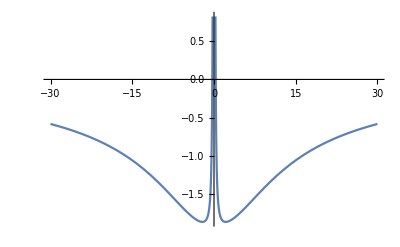

o29=pow(r,-2.);
o35=x*x;
o44=o29*o35;
o8=ma*ma;
o45=o44+o8;
o46=1./sqrt(o45);
o52=mb*mb;
o53=o44+o52;
o54=1./sqrt(o53);
o60=r*r;
o61=o60*o8;
o104=sqrt(o45);
o105=sqrt(o53);
o114=1/r;
o62=o35+o61;
o103=1/o62;
init0=-o46-o54+2.*G*o114*o52*o8*(1.-2.*pow(ma,-2.)*pow(mb,-2.)*pow(o104*o105+o44,2.))*pow(o\
45,-2.)+4.*G*o103*o46*o54*(o35+o104*o105*o60)*(2.*o35+2.*o104*o105*o60+o52*o60+o61)*pow(r,\
-3.)+G*o103*o114*pow(x,-2.)*(2.*o35*o60*(2.*o104*o105+o52+o8)+o52*o8*pow(r,4.)+4.*pow(x,4.\
));

o8=pow(r,-2.);
o35=x*x;
o44=o35*o8;
o29=ma*ma;
o45=o29+o44;
o52=mb*mb;
o53=o44+o52;
o62=sqrt(o45);
o106=sqrt(o53);
o105=1./sqrt(o45);
o103=1./sqrt(o53);
o114=r*r;
o113=pow(r,-3.);
o115=o114*o29;
o116=o115+o35;
o117=1/o116;
o54=pow(o53,-1.5);
o123=o106*o114*o62;
o124=o123+o35;
o132=o114*o52;
o133=2.*o35;
o134=2.*o106*o114*o62;
o135=o115+o132+o133+o134;
o137=pow(r,-5.);
o46=pow(o45,-1.5);
o110=o106*o62;
o111=o110+o44;
o59=1/r;
o152=pow(o116,-2.);
o169=2.*o106*o62;
o170=o169+o29+o52;
o197=pow(r,4.);
o198=o197*o29*o52;
o199=pow(x,4.);
o203=4.*o199;
o204=2.*o114*o170*o35;
o205=o198+o203+o204;
init0prime=(-2.*G*o152*o205*o59)/x-8.*G*o103*o105*o113*o124*o135*o152*x-4.*G*o103*o117*o124\
*o135*o137*o46*x-4.*G*o105*o117*o124*o135*o137*o54*x+o46*o8*x+o54*o8*x+4.*G*o103*o105*o113\
*o117*o135*(2.*x+o105*o106*x+o103*o62*x)+4.*G*o103*o105*o113*o117*o124*(4.*x+2.*o105*o106*\
x+2.*o103*o62*x)-8.*G*o113*o29*o52*x*(1.-2.*(o111*o111)*pow(ma,-2.)*pow(mb,-2.))*pow(o45,-\
3.)-8.*G*o111*o59*(2.*o8*x+o105*o106*o8*x+o103*o62*o8*x)*pow(o45,-2.)-2.*G*o117*o205*o59*p\
ow(x,-3.)+G*o117*o59*pow(x,-2.)*(4.*o114*o170*x+2.*o114*o35*(2.*o105*o106*o8*x+2.*o103*o62\
*o8*x)+16.*pow(x,3.));

o29=x*x;
o44=pow(r,-2.);
o35=ma*ma;
o45=o29*o44;
o46=o35+o45;
o8=pow(r,-4.);
o58=mb*mb;
o59=o45+o58;
o111=1./sqrt(o59);
o110=1./sqrt(o46);
o113=sqrt(o46);
o115=sqrt(o59);
o124=1/r;
o126=pow(o46,-2.);
o62=pow(o59,-1.5);
o53=pow(o46,-1.5);
o104=pow(r,-3.);
o127=2.*o44*x;
o129=o111*o113*o44*x;
o130=o110*o115*o44*x;
o131=o127+o129+o130;
o153=o113*o115;
o154=o153+o45;
o105=r*r;
o106=o105*o35;
o108=o106+o29;
o109=1/o108;
o118=4.*x;
o119=2.*o111*o113*x;
o121=2.*o110*o115*x;
o122=o118+o119+o121;
o165=o105*o113*o115;
o166=o165+o29;
o168=pow(r,-5.);
o112=2.*x;
o114=o111*o113*x;
o116=o110*o115*x;
o117=o112+o114+o116;
o204=o105*o58;
o205=2.*o29;
o206=2.*o105*o113*o115;
o207=o106+o204+o205+o206;
o171=pow(o108,-2.);
o60=pow(o59,-2.5);
o213=pow(r,-7.);
o47=pow(o46,-2.5);
o156=pow(o46,-3.);
o225=pow(ma,-2.);
o226=pow(mb,-2.);
o227=o154*o154;
o228=-2.*o225*o226*o227;
o229=1.+o228;
o244=2.*o111*o113*o44*x;
o245=2.*o110*o115*o44*x;
o246=o244+o245;
o248=2.*o113*o115;
o249=o248+o35+o58;
o254=pow(x,3.);
o255=16.*o254;
o256=2.*o105*o246*o29;
o257=4.*o105*o249*x;
o258=o255+o256+o257;
o221=pow(o108,-3.);
o232=pow(x,-2.);
o262=pow(r,4.);
o263=o262*o35*o58;
o265=pow(x,4.);
o266=4.*o265;
o267=2.*o105*o249*o29;
o268=o263+o266+o267;
init0prime2=8.*G*o104*o109*o110*o111*o117*o122-8.*G*o104*o110*o111*o166*o171*o207+8.*G*o124\
*o221*o268+6.*G*o124*o171*o232*o268+32.*G*o104*o110*o111*o166*o207*o221*o29+12.*G*o109*o11\
1*o166*o207*o213*o29*o47-4.*G*o109*o111*o166*o168*o207*o53+16.*G*o111*o166*o168*o171*o207*\
o29*o53+o44*o53-8.*G*o104*o156*o229*o35*o58+12.*G*o109*o110*o166*o207*o213*o29*o60-4.*G*o1\
09*o110*o166*o168*o207*o62+16.*G*o110*o166*o168*o171*o207*o29*o62+o44*o62+8.*G*o109*o166*o\
207*o213*o29*o53*o62+4.*G*o104*o109*o110*o111*o166*(4.+2.*o111*o113+2.*o110*o115+4.*o110*o\
111*o29*o44-2.*o115*o29*o44*o53-2.*o113*o29*o44*o62)+4.*G*o104*o109*o110*o111*o207*(2.+o11\
1*o113+o110*o115+2.*o110*o111*o29*o44-o115*o29*o44*o53-o113*o29*o44*o62)-3.*o29*o47*o8-3.*\
o29*o60*o8-8.*G*o124*o126*o154*(2.*o44+o111*o113*o44+o110*o115*o44+2.*o110*o111*o29*o8-o11\
5*o29*o53*o8-o113*o29*o62*o8)-(4.*G*o124*o171*o258)/x+64.*G*o104*o131*o154*o156*x-16.*G*o1\
04*o110*o111*o122*o166*o171*x-16.*G*o104*o110*o111*o117*o171*o207*x-8.*G*o109*o111*o122*o1\
66*o168*o53*x-8.*G*o109*o111*o117*o168*o207*o53*x-8.*G*o109*o110*o122*o166*o168*o62*x-8.*G\
*o109*o110*o117*o168*o207*o62*x+G*o109*o124*o232*(4.*o105*o249+48.*o29+2.*o105*o29*(2.*o11\
1*o113*o44+2.*o110*o115*o44+4.*o110*o111*o29*o8-2.*o115*o29*o53*o8-2.*o113*o29*o62*o8)+8.*\
o105*o246*x)-8.*G*o124*o126*(o131*o131)+48.*G*o168*o229*o29*o35*o58*pow(o46,-4.)+6.*G*o109\
*o124*o268*pow(x,-4.)-4.*G*o109*o124*o258*pow(x,-3.);

init0.txt

initprime.txt

initprime2.txt

```mathematica
init0=(init[x] r^3)/x^2/.pθ->x//Simplify
Plot[init0/.{r->userr,ma->userm1,mb->userm2,G->userG},{x,-30,30}]
init0prime=D[init0,x];
init0prime2=D[init0prime,x];
initc=CAssign[init0,init0,"OptimizationSymbol"->o]
initcprime=CAssign[init0prime,init0prime,"OptimizationSymbol"->o]
initcprime2=CAssign[init0prime2,init0prime2,"OptimizationSymbol"->o]
Export["init0.txt",initc]
Export["initprime.txt",initcprime]
Export["initprime2.txt",initcprime2]
```

### Schwarzschild Solution

Many papers posit that using the Schwarzschild solution to solve for the angular momentum in a conserved system works for a Post-Minkowski approximation.

```mathematica
rs=(2G M)/c^2
Lz=√((μ^2 c^2 rs r^2)/(2r-3rs))//Simplify
solutionSchwarzschild=Lz/.{c->userC,G->userG,ma->userm1,mb->userm2,r->userr}//N
%/newtonianZero[[1,1]]//N
```

(2 G (ma+mb))/c^2

√(-(c^2 G ma^2 mb^2 r^2)/((ma+mb) (3 G (ma+mb)-c^2 r)))

0.317291

1.00602

### Schaefer Solution

This is simply taking the N-body Hamiltonian that’s derived in this paper, and solving it for initial data by itself.

(-pθ^2 (√(ma^2+pθ^2/r^2)+√(mb^2+pθ^2/r^2)) (r^2)^(3/2) (pθ^2+ma^2 r^2) (pθ^2+mb^2 r^2)+G (12 pθ^8+6 ma^2 mb^2 pθ^2 (ma^2+mb^2+2 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2)) r^6+ma^4 mb^4 r^8+pθ^6 (18 ma^2 r^2+18 mb^2 r^2+12 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^2)+pθ^4 (4 ma^4 r^4+4 mb^4 r^4+12 mb^2 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^4+ma^2 (27 mb^2 r^4+12 √(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^4))))/(√(ma^2+pθ^2/r^2) √(mb^2+pθ^2/r^2) r^5 √(r^2) (pθ^2+ma^2 r^2) (pθ^2+mb^2 r^2))

(125000+3 pθ^6-200 pθ^4 (-3+2 π √(100+pθ^2))-1250 pθ^2 (-23+32 π √(100+pθ^2)))/(20000 π (100+pθ^2)^2)

{{pθ→-√(Root0.102Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,3]0.10164729316990495)},{pθ→√(Root0.102Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,3]0.10164729316990495)},{pθ→-√(Root1.75 × 10^5Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,4]175359.63854386608)},{pθ→√(Root1.75 × 10^5Root[15625000000+7187500000 #1+(976562500-160000000000 π^2) #1^2+(35250000-4800000000 π^2) #1^3+(532500-48000000 π^2) #1^4+(3600-160000 π^2) #1^5+9 #1^6&,4]175359.63854386608)}}

0.318822

0.0318821726314103251509579

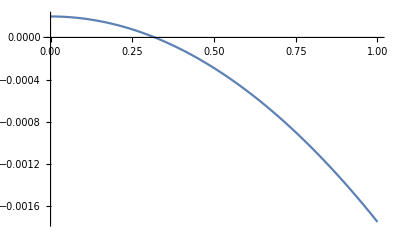

```mathematica
PM1/.{qax->r Cos[θ]+qbx,qay->r Sin[θ]+qby,pax->pcan Cos[θ],pay->pcan Sin[θ],pbx->-pcan Cos[θ],pby->-pcan Sin[θ]};
%/.pcan->√(pr^2+pθ^2/r^2);
PM1rdot[pθ_]=D[%,r];
PM1rdot[pθ]/.{pr->0,θ->0}//Simplify
%/.{ma->userm1,mb->userm2,G->userG,r->userr}//Simplify
Solve[%==0,pθ,Reals]
solutionSchaefer=pθ/.%[[2,1]]//N
N[(pθ/.%%[[2,1]])/userr,25]
Plot[PM1rdot[pθ]/.{pr->0,θ->0,ma->userm1,mb->userm2,G->userG,r->userr},{pθ,0,1}]



(*PM1/.{qay->0,qby->0,pax->0,pbx->0,pby->-pay,qax->r+qbx}
PM1rdot=D[%,r]
PM1rdot/.{ma->userm1,mb->userm2,G->userG,r->userr}//Simplify
Solve[%==0,pay,Reals]*)
```

### Comparison

```mathematica
solutionAntonelli
solutionBern
solutionSchwarzschild
solutionSchaefer
```

0.317291

0.318822

0.317291

0.318822

## Checking Julia Code

This is to double check that the Julia code is functioning correctly and check it against the Mathematica code.

### Post-Minkowski Hamiltonian

```mathematica
oo3=ma*ma;
oo4=pax*pax;
oo5=pay*pay;
oo6=oo3+oo4+oo5;
oo7=√oo6;
oo8=mb*mb;
oo9=pbx*pbx;
oo10=pby*pby;
oo11=oo10+oo8+oo9;
oo12=√oo11;
oo13=oo4+oo5;
oo14=1/o6;
oo15=oo13*oo14;
oo16=oo10+oo9;
oo17=1/oo11;
oo18=oo16*oo17;
oo19=1+oo15+oo18;
oo20=-qbx;
oo21=oo20+qax;
oo22=oo21*oo21;
oo23=-qby;
oo24=oo23+qay;
oo25=oo24*oo24;
oo26=oo22+oo25;
oo27=1/√oo26;
oo29=-qax;
oo30=oo29+qbx;
oo31=oo30*oo30;
oo32=-qay;
oo33=oo32+qby;
oo34=oo33*oo33;
oo35=oo31+oo34;
oo36=1/√oo35;
oo40=pax*pbx;
oo41=pay*pby;
oo42=oo40+oo41;
oo43=7*oo42;
oo44=oo21*oo27*pax;
oo45=oo24*oo27*pay;
oo46=oo44+oo45;
oo72=oo42*oo42;
oo66=oo46*oo46;
oo47=oo21*oo27*pbx;
oo48=oo24*oo27*pby;
oo49=oo47+oo48;
oo65=1/√oo6;
oo67=oo3+oo66;
oo68=√oo67;
oo77=oo49*oo49;
oo85=oo66*oo77;
oo56=oo30*oo36*pbx;
oo57=oo33*oo36*pby;
oo58=oo56+oo57;
oo64=1/√oo11;
oo99=oo58*oo58;
oo100=oo8+oo99;
oo53=oo30*oo36*pax;
oo54=oo33*oo36*pay;
oo55=oo53+oo54;
oo108=oo55*oo55;
oo102=√oo100;
oo81=oo13*oo16;
oo120=oo108*oo99;

juliaPM1=oo12+0.25*G*(oo27*(oo43+oo46*oo49)+oo36*(oo43+oo55*oo58))+oo7-0.5*G*(oo12*oo19*oo27*oo7+oo12*oo19*oo36*oo7)-0.25*G*((1*oo27*oo65*(oo102*oo64*(oo120-3*oo108*oo16+8*oo42*oo55*oo58+oo81-3*oo13*oo99)+2*(oo120-oo108*oo16+2*oo42*oo55*oo58+oo72+(-oo4-oo5)*oo99)+2*oo17*(-2*oo16*oo42*oo55*oo58-oo16*oo72+2*oo72*oo99+oo108*(oo16*oo16)))*((1+oo102*oo64)^-2))/√oo100+(1*oo36*oo64*(oo65*oo68*(8*oo42*oo46*oo49-3*oo16*oo66-3*oo13*oo77+oo81+oo85)+2*(2*oo42*oo46*oo49+oo72-oo13*oo77+oo85+oo66*(-oo10-oo9))+2*oo14*(-2*oo13*oo42*oo46*oo49-oo13*oo72+2*oo66*oo72+oo77*(oo13*oo13)))*((1+oo65*oo68)^-2))/√oo67);
juliaPM1==PM1
```

True

### Derivatives

```mathematica
o3=ma*ma;
o4=pax*pax;
o5=pay*pay;
o6=o3+o4+o5;
o7=1/√o6;
o16=mb*mb;
o17=pbx*pbx;
o18=pby*pby;
o19=o16+o17+o18;
o20=√o19;
o10=o4+o5;
o13=1/o6;
o21=-qbx;
o22=o21+qax;
o23=o22*o22;
o24=-qby;
o25=o24+qay;
o26=o25*o25;
o27=o23+o26;
o28=1/√o27;
o9=√o6;
o11=o6^-2;
o12=-2*o10*o11*pax;
o14=2*o13*pax;
o15=o12+o14;
o30=o10*o13;
o31=o17+o18;
o32=1/o19;
o33=o31*o32;
o34=1+o30+o33;
o36=-qax;
o37=o36+qbx;
o38=o37*o37;
o39=-qay;
o40=o39+qby;
o41=o40*o40;
o42=o38+o41;
o43=1/√o42;
o48=7*pbx;
o73=pax*pbx;
o74=pay*pby;
o75=o73+o74;
o76=o75*o75;
o64=o22*o28*pax;
o65=o25*o28*pay;
o66=o64+o65;
o67=o66*o66;
o49=o22*o28*pbx;
o50=o25*o28*pby;
o51=o49+o50;
o68=o3+o67;
o69=√o68;
o81=o51*o51;
o89=o67*o81;
o101=1/√o68;
o63=1/√o19;
o70=o69*o7;
o71=1+o70;
o77=-(o10*o76);
o78=2*o67*o76;
o79=-2*o10*o51*o66*o75;
o80=o10*o10;
o82=o80*o81;
o83=o77+o78+o79+o82;
o102=o6^-1.5;
o85=o10*o31;
o86=-3*o31*o67;
o87=8*o51*o66*o75;
o88=-3*o10*o81;
o90=o85+o86+o87+o88+o89;
o92=-o17;
o93=-o18;
o94=o92+o93;
o125=2*o22*o28*o66*o81;
o107=o71^-2;
o84=2*o13*o83;
o91=o69*o7*o90;
o95=o67*o94;
o96=2*o51*o66*o75;
o97=-(o10*o81);
o98=o76+o89+o95+o96+o97;
o99=2*o98;
o100=o84+o91+o99;
o55=o37*o43*pbx;
o56=o40*o43*pby;
o57=o55+o56;
o140=o57*o57;
o141=o140+o16;
o149=o37*o43*pax;
o150=o40*o43*pay;
o151=o149+o150;
o143=√o141;
o128=2*o31*pax;
o120=2*o75*pbx;
o162=2*o140*o151*o37*o43;
o142=1/√o141;
o144=o143*o63;
o145=1+o144;
o146=o145^-2;
o148=o31*o31;
o174=o151*o151;
o186=o140*o174;
o200=-2*o10*o11*pay;
o201=2*o13*pay;
o202=o200+o201;
o209=7*pby;
o72=o71^-3;
o239=2*o25*o28*o66*o81;
o138=o68^-1.5;
o242=2*o31*pay;
o234=2*o75*pby;
o264=2*o140*o151*o40*o43;
o173=-(o31*o76);
o175=o148*o174;
o176=-2*o151*o31*o57*o75;
o177=2*o140*o76;
o178=o173+o175+o176+o177;
o179=2*o178*o32;
o180=-(o174*o31);
o181=2*o151*o57*o75;
o182=-o4;
o183=-o5;
o184=o182+o183;
o185=o140*o184;
o187=o180+o181+o185+o186+o76;
o188=2*o187;
o189=-3*o174*o31;
o190=8*o151*o57*o75;
o191=-3*o10*o140;
o192=o186+o189+o190+o191+o85;
o193=o143*o192*o63;
o194=o179+o188+o193;
o280=o19^-2;
o281=-2*o280*o31*pbx;
o282=2*o32*pbx;
o283=o281+o282;
o290=7*pax;
o313=2*o22*o28*o51*o67;
o316=2*o75*pax;
o308=2*o10*pbx;
o329=2*o174*o37*o43*o57;
o299=o19^-1.5;
o364=-2*o280*o31*pby;
o365=2*o32*pby;
o366=o364+o365;
o373=7*pay;
o395=2*o25*o28*o51*o67;
o398=2*o75*pay;
o390=2*o10*pby;
o411=2*o174*o40*o43*o57;
o356=o145^-3;
o358=o141^-1.5;
o443=o27^-1.5;
o445=o42^-1.5;
o449=7*o75;
o458=-(o23*o443*pax);
o459=o28*pax;
o460=-(o22*o25*o443*pay);
o461=o458+o459+o460;
o453=-(o23*o443*pbx);
o454=o28*pbx;
o455=-(o22*o25*o443*pby);
o456=o453+o454+o455;
o493=2*o456*o51*o67;
o494=2*o461*o66*o81;
o470=o38*o445*pax;
o471=o37*o40*o445*pay;
o472=-(o43*pax);
o473=o470+o471+o472;
o465=o38*o445*pbx;
o466=o37*o40*o445*pby;
o467=-(o43*pbx);
o468=o465+o466+o467;
o519=2*o174*o468*o57;
o520=2*o140*o151*o473;
o450=o51*o66;
o451=o449+o450;
o477=o151*o57;
o478=o449+o477;
o543=o28*pay;
o544=-(o22*o25*o443*pax);
o545=-(o26*o443*pay);
o546=o543+o544+o545;
o548=o28*pby;
o549=-(o22*o25*o443*pbx);
o550=-(o26*o443*pby);
o551=o548+o549+o550;
o580=2*o546*o66*o81;
o583=2*o51*o551*o67;
o507=1/o68;
o561=o37*o40*o445*pax;
o562=o41*o445*pay;
o563=-(o43*pay);
o564=o561+o562+o563;
o556=o37*o40*o445*pbx;
o557=o41*o445*pby;
o558=-(o43*pby);
o559=o556+o557+o558;
o607=2*o174*o559*o57;
o608=2*o140*o151*o564;
o532=1/o141;
o636=o23*o443*pax;
o637=-(o28*pax);
o638=o22*o25*o443*pay;
o639=o636+o637+o638;
o631=o23*o443*pbx;
o632=-(o28*pbx);
o633=o22*o25*o443*pby;
o634=o631+o632+o633;
o669=2*o51*o634*o67;
o670=2*o639*o66*o81;
o648=-(o38*o445*pax);
o649=-(o37*o40*o445*pay);
o650=o43*pax;
o651=o648+o649+o650;
o643=-(o38*o445*pbx);
o644=-(o37*o40*o445*pby);
o645=o43*pbx;
o646=o643+o644+o645;
o694=2*o174*o57*o646;
o695=2*o140*o151*o651;
o717=-(o28*pay);
o718=o22*o25*o443*pax;
o719=o26*o443*pay;
o720=o717+o718+o719;
o722=-(o28*pby);
o723=o22*o25*o443*pbx;
o724=o26*o443*pby;
o725=o722+o723+o724;
o754=2*o66*o720*o81;
o757=2*o51*o67*o725;
o735=-(o37*o40*o445*pax);
o736=-(o41*o445*pay);
o737=o43*pay;
o738=o735+o736+o737;
o730=-(o37*o40*o445*pbx);
o731=-(o41*o445*pby);
o732=o43*pby;
o733=o730+o731+o732;
o781=2*o174*o57*o733;
o782=2*o140*o151*o738;

juliaPM1second=o20+0.25*G*(o28*o451+o43*o478)-0.25*G*(o100*o101*o107*o43*o63+o142*o146*o194*o28*o7)+o9-0.5*G*(o20*o28*o34*o9+o20*o34*o43*o9);

juliadqax=0.25*G*(o28*(o48+o22*o28*o51)+o43*(o48+o37*o43*o57))+o7*pax-0.5*G*(o15*o20*o28*o9+o15*o20*o43*o9+o20*o28*o34*o7*pax+o20*o34*o43*o7*pax)-0.25*G*(-(o100*o107*o138*o22*o28*o43*o63*o66)-o102*o142*o146*o194*o28*pax-2*o100*o101*o43*o63*o72*(o101*o22*o28*o66*o7-o102*o69*pax)+o142*o146*o28*o7*(2*(o120+o162-2*o151*o31*o37*o43+2*o37*o43*o57*o75-2*o140*pax+2*o151*o57*pbx)+o143*o63*(o128+o162-6*o151*o31*o37*o43+8*o37*o43*o57*o75-6*o140*pax+8*o151*o57*pbx)+2*o32*(2*o148*o151*o37*o43-2*o31*o37*o43*o57*o75-2*o151*o31*o57*pbx+4*o140*o75*pbx-2*o31*o75*pbx))+o101*o107*o43*o63*(o101*o22*o28*o66*o7*o90-4*o11*o83*pax-o102*o69*o90*pax+2*(o120+o125+2*o22*o28*o51*o75+2*o22*o28*o66*o94-2*o81*pax+2*o51*o66*pbx)+o69*o7*(o125+o128-6*o22*o28*o31*o66+8*o22*o28*o51*o75-6*o81*pax+8*o51*o66*pbx)+2*o13*(-2*o10*o22*o28*o51*o75+4*o22*o28*o66*o76-4*o51*o66*o75*pax-2*o76*pax+4*o10*o81*pax-2*o10*o51*o66*pbx-2*o10*o75*pbx+4*o67*o75*pbx)));
juliadqay=0.25*G*(o28*(o209+o25*o28*o51)+o43*(o209+o40*o43*o57))+o7*pay-0.5*G*(o20*o202*o28*o9+o20*o202*o43*o9+o20*o28*o34*o7*pay+o20*o34*o43*o7*pay)-0.25*G*(-(o100*o107*o138*o25*o28*o43*o63*o66)-o102*o142*o146*o194*o28*pay-2*o100*o101*o43*o63*o72*(o101*o25*o28*o66*o7-o102*o69*pay)+o142*o146*o28*o7*(2*(o234+o264-2*o151*o31*o40*o43+2*o40*o43*o57*o75-2*o140*pay+2*o151*o57*pby)+o143*o63*(o242+o264-6*o151*o31*o40*o43+8*o40*o43*o57*o75-6*o140*pay+8*o151*o57*pby)+2*o32*(2*o148*o151*o40*o43-2*o31*o40*o43*o57*o75-2*o151*o31*o57*pby+4*o140*o75*pby-2*o31*o75*pby))+o101*o107*o43*o63*(o101*o25*o28*o66*o7*o90-4*o11*o83*pay-o102*o69*o90*pay+2*(o234+o239+2*o25*o28*o51*o75+2*o25*o28*o66*o94-2*o81*pay+2*o51*o66*pby)+o69*o7*(o239+o242-6*o25*o28*o31*o66+8*o25*o28*o51*o75-6*o81*pay+8*o51*o66*pby)+2*o13*(-2*o10*o25*o28*o51*o75+4*o25*o28*o66*o76-4*o51*o66*o75*pay-2*o76*pay+4*o10*o81*pay-2*o10*o51*o66*pby-2*o10*o75*pby+4*o67*o75*pby)));
juliadpax=-0.25*G*(-(o22*o443*o451)+o37*o445*o478+o43*(o151*o468+o473*o57)+o28*(o461*o51+o456*o66))+0.5*G*(-(o20*o22*o34*o443*o9)+o20*o34*o37*o445*o9)+0.25*G*(o100*o101*o107*o37*o445*o63-o100*o107*o138*o43*o461*o63*o66-o142*o146*o194*o22*o443*o7-o146*o194*o28*o358*o468*o57*o7-2*o194*o28*o356*o468*o532*o57*o63*o7-2*o100*o43*o461*o507*o63*o66*o7*o72+o142*o146*o28*o7*(o142*o192*o468*o57*o63+2*(-2*o151*o31*o473+o519+o520+2*o184*o468*o57+2*o151*o468*o75+2*o473*o57*o75)+o143*o63*(-6*o151*o31*o473+o519+o520-6*o10*o468*o57+8*o151*o468*o75+8*o473*o57*o75)+2*o32*(2*o148*o151*o473-2*o151*o31*o468*o75-2*o31*o473*o57*o75+4*o468*o57*o76))+o101*o107*o43*o63*(o69*o7*(o493+o494-6*o10*o456*o51-6*o31*o461*o66+8*o461*o51*o75+8*o456*o66*o75)+2*o13*(-2*o10*o461*o51*o75-2*o10*o456*o66*o75+4*o461*o66*o76+2*o456*o51*o80)+o101*o461*o66*o7*o90+2*(o493+o494-2*o10*o456*o51+2*o461*o51*o75+2*o456*o66*o75+2*o461*o66*o94)));
juliadpay=-0.25*G*(-(o25*o443*o451)+o40*o445*o478+o43*(o151*o559+o564*o57)+o28*(o51*o546+o551*o66))+0.5*G*(-(o20*o25*o34*o443*o9)+o20*o34*o40*o445*o9)+0.25*G*(o100*o101*o107*o40*o445*o63-o100*o107*o138*o43*o546*o63*o66-o142*o146*o194*o25*o443*o7-o146*o194*o28*o358*o559*o57*o7-2*o194*o28*o356*o532*o559*o57*o63*o7-2*o100*o43*o507*o546*o63*o66*o7*o72+o142*o146*o28*o7*(o142*o192*o559*o57*o63+2*(-2*o151*o31*o564+2*o184*o559*o57+o607+o608+2*o151*o559*o75+2*o564*o57*o75)+o143*o63*(-6*o151*o31*o564-6*o10*o559*o57+o607+o608+8*o151*o559*o75+8*o564*o57*o75)+2*o32*(2*o148*o151*o564-2*o151*o31*o559*o75-2*o31*o564*o57*o75+4*o559*o57*o76))+o101*o107*o43*o63*(o69*o7*(-6*o10*o51*o551+o580+o583-6*o31*o546*o66+8*o51*o546*o75+8*o551*o66*o75)+2*o13*(-2*o10*o51*o546*o75-2*o10*o551*o66*o75+4*o546*o66*o76+2*o51*o551*o80)+o101*o546*o66*o7*o90+2*(-2*o10*o51*o551+o580+o583+2*o51*o546*o75+2*o551*o66*o75+2*o546*o66*o94)));

juliadqbx=0.25*G*(o43*(o290+o151*o37*o43)+o28*(o290+o22*o28*o66))+o63*pbx-0.5*G*(o20*o28*o283*o9+o20*o283*o43*o9+o28*o34*o63*o9*pbx+o34*o43*o63*o9*pbx)-0.25*G*(-(o146*o194*o28*o358*o37*o43*o57*o7)-o100*o101*o107*o299*o43*pbx-2*o142*o194*o28*o356*o7*(o142*o37*o43*o57*o63-o143*o299*pbx)+o101*o107*o43*o63*(2*o13*(-2*o10*o22*o28*o66*o75+2*o22*o28*o51*o80-2*o10*o51*o66*pax-2*o10*o75*pax+4*o67*o75*pax)+o69*o7*(o308+o313-6*o10*o22*o28*o51+8*o22*o28*o66*o75+8*o51*o66*pax-6*o67*pbx)+2*(o313+o316-2*o10*o22*o28*o51+2*o22*o28*o66*o75+2*o51*o66*pax-2*o67*pbx))+o142*o146*o28*o7*(o142*o192*o37*o43*o57*o63-4*o178*o280*pbx-o143*o192*o299*pbx+o143*o63*(o308+o329-6*o10*o37*o43*o57+8*o151*o37*o43*o75+8*o151*o57*pax-6*o174*pbx)+2*(o316+o329+2*o184*o37*o43*o57+2*o151*o37*o43*o75+2*o151*o57*pax-2*o174*pbx)+2*o32*(-2*o151*o31*o37*o43*o75+4*o37*o43*o57*o76-2*o151*o31*o57*pax+4*o140*o75*pax-2*o31*o75*pax+4*o174*o31*pbx-4*o151*o57*o75*pbx-2*o76*pbx)));
juliadqby=0.25*G*(o43*(o373+o151*o40*o43)+o28*(o373+o25*o28*o66))+o63*pby-0.5*G*(o20*o28*o366*o9+o20*o366*o43*o9+o28*o34*o63*o9*pby+o34*o43*o63*o9*pby)-0.25*G*(-(o146*o194*o28*o358*o40*o43*o57*o7)-o100*o101*o107*o299*o43*pby-2*o142*o194*o28*o356*o7*(o142*o40*o43*o57*o63-o143*o299*pby)+o101*o107*o43*o63*(2*o13*(-2*o10*o25*o28*o66*o75+2*o25*o28*o51*o80-2*o10*o51*o66*pay-2*o10*o75*pay+4*o67*o75*pay)+o69*o7*(o390+o395-6*o10*o25*o28*o51+8*o25*o28*o66*o75+8*o51*o66*pay-6*o67*pby)+2*(o395+o398-2*o10*o25*o28*o51+2*o25*o28*o66*o75+2*o51*o66*pay-2*o67*pby))+o142*o146*o28*o7*(o142*o192*o40*o43*o57*o63-4*o178*o280*pby-o143*o192*o299*pby+o143*o63*(o390+o411-6*o10*o40*o43*o57+8*o151*o40*o43*o75+8*o151*o57*pay-6*o174*pby)+2*(o398+o411+2*o184*o40*o43*o57+2*o151*o40*o43*o75+2*o151*o57*pay-2*o174*pby)+2*o32*(-2*o151*o31*o40*o43*o75+4*o40*o43*o57*o76-2*o151*o31*o57*pay+4*o140*o75*pay-2*o31*o75*pay+4*o174*o31*pby-4*o151*o57*o75*pby-2*o76*pby)));
juliadpbx=-0.25*G*(o22*o443*o451-o37*o445*o478+o43*(o151*o646+o57*o651)+o28*(o51*o639+o634*o66))+0.5*G*(o20*o22*o34*o443*o9-o20*o34*o37*o445*o9)+0.25*G*(-(o100*o101*o107*o37*o445*o63)-o100*o107*o138*o43*o63*o639*o66+o142*o146*o194*o22*o443*o7-o146*o194*o28*o358*o57*o646*o7-2*o194*o28*o356*o532*o57*o63*o646*o7-2*o100*o43*o507*o63*o639*o66*o7*o72+o142*o146*o28*o7*(o142*o192*o57*o63*o646+2*(2*o184*o57*o646-2*o151*o31*o651+o694+o695+2*o151*o646*o75+2*o57*o651*o75)+o143*o63*(-6*o10*o57*o646-6*o151*o31*o651+o694+o695+8*o151*o646*o75+8*o57*o651*o75)+2*o32*(2*o148*o151*o651-2*o151*o31*o646*o75-2*o31*o57*o651*o75+4*o57*o646*o76))+o101*o107*o43*o63*(o69*o7*(-6*o10*o51*o634-6*o31*o639*o66+o669+o670+8*o51*o639*o75+8*o634*o66*o75)+2*o13*(-2*o10*o51*o639*o75-2*o10*o634*o66*o75+4*o639*o66*o76+2*o51*o634*o80)+o101*o639*o66*o7*o90+2*(-2*o10*o51*o634+o669+o670+2*o51*o639*o75+2*o634*o66*o75+2*o639*o66*o94)));
juliadpby=-0.25*G*(o25*o443*o451-o40*o445*o478+o28*(o51*o720+o66*o725)+o43*(o151*o733+o57*o738))+0.5*G*(o20*o25*o34*o443*o9-o20*o34*o40*o445*o9)+0.25*G*(-(o100*o101*o107*o40*o445*o63)+o142*o146*o194*o25*o443*o7-o100*o107*o138*o43*o63*o66*o720-2*o100*o43*o507*o63*o66*o7*o72*o720-o146*o194*o28*o358*o57*o7*o733-2*o194*o28*o356*o532*o57*o63*o7*o733+o142*o146*o28*o7*(o142*o192*o57*o63*o733+2*o32*(2*o148*o151*o738-2*o151*o31*o733*o75-2*o31*o57*o738*o75+4*o57*o733*o76)+2*(2*o184*o57*o733-2*o151*o31*o738+2*o151*o733*o75+2*o57*o738*o75+o781+o782)+o143*o63*(-6*o10*o57*o733-6*o151*o31*o738+8*o151*o733*o75+8*o57*o738*o75+o781+o782))+o101*o107*o43*o63*(o69*o7*(-6*o31*o66*o720-6*o10*o51*o725+8*o51*o720*o75+8*o66*o725*o75+o754+o757)+2*o13*(-2*o10*o51*o720*o75-2*o10*o66*o725*o75+4*o66*o720*o76+2*o51*o725*o80)+o101*o66*o7*o720*o90+2*(-2*o10*o51*o725+2*o51*o720*o75+2*o66*o725*o75+o754+o757+2*o66*o720*o94)));

juliaPM1second==PM1
juliadqax==D[PM1,pax]
juliadqay==D[PM1,pay]
juliadpax==-D[PM1,qax]
juliadpay==-D[PM1,qay]
juliadqbx==D[PM1,pbx]
juliadqby==D[PM1,pby]
juliadpbx==-D[PM1,qbx]
juliadpby==-D[PM1,qby]
```

True

True

True

«6 more identical outputs»